```mathematica
(*setup information*)
h= 1 /100; 
λ=500;
a0= 1; 
c= 0;
```

```mathematica
varC[t_] = 1000*Sin[Pi t]^6
```

1000 Sin[π t]^6

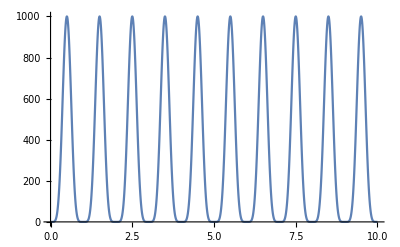

```mathematica
Plot[varC[t], {t, 0, 10}]
```

```mathematica
theoSol = DSolve[{a''[t]+λ a[t]+varC[t]==0,a[0]==a0,a'[0]==0},a[t],t];
```

```mathematica
theoα[t_] = (a[t]/.theoSol[[1]]) // FullSimplify
```

(8 (-3906250+437500 π^2-12250 π^4+117 π^6) Cos[10 √5 t]+5 (-125+9 π^2) (375 (125-4 π^2) Cos[2 π t]+2 (-125+π^2) (125-4 π^2+75 Cos[4 π t]))-125 (-125+π^2) (-125+4 π^2) Cos[6 π t])/(16 (-125+π^2) (-125+4 π^2) (-125+9 π^2))

```mathematica
theoα[t] // N
```

-1.75478×10^-7 (-180.868 (32070.6 Cos[6.28319 t]-230.261 (85.5216+75. Cos[12.5664 t]))-1.23077×10^6 Cos[18.8496 t]-5.35262×10^6 Cos[22.3607 t])

```mathematica
oldα[t_] = (a0 + c / λ) Cos[Sqrt[λ]t] - c / λ
```

Cos[10 √5 t]

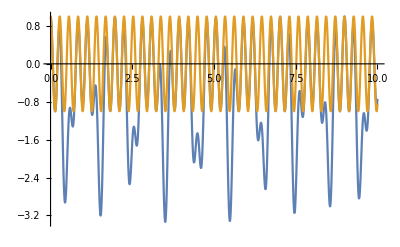

```mathematica
Plot[{theoα[t], oldα[t]}, {t, 0, 10}]
```

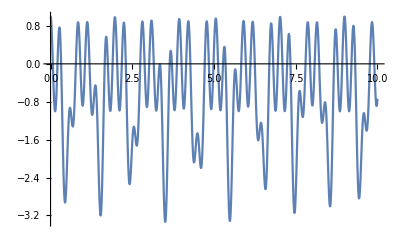

```mathematica
Plot[{theoα[t]}, {t, 0, 10}]
```

```mathematica
theoα[8]// N
```

-0.862447

```mathematica
(*Theoretic Solution*)
```

```mathematica
(*Implicit Euler*)
M = {{1, -h},{λ h, 1}};
w1[n_]= {0, -h varC[n h ]};
A = Inverse[M];
 w[n_]= A.w1[n];
IEα = {a0};
IEβ = {0};

For[i=1,i≤100,
a =A[[1,1]] IEα[[i]] + A[[1,2]] IEβ[[i]] + w[i][[1]];
 b=A[[2,1]] IEα[[i]] + A[[2,2]] IEβ[[i]] + w[i][[2]];
AppendTo[IEα, a];
AppendTo[IEβ, b];
i++] ;
```

```mathematica
IEα[[1]]
```

$Aborted[]

```mathematica
ListPlot[IEα]
```

```mathematica
Norm[2(10-ⅈ √5) / 21]
```

2 √(5/21)

```mathematica
(*Newmark-β*)
(*M = {{1 + h^2 λ β, 0},{λ h / 2, 1}};
w = {-h^2c / 2, - h c};
M1 ={{1 - h ^2 λ(1/2 - β), h}, {-λ h / 2, 1}}
A = Inverse[M].M1;
w = Inverse[M].w;
sol = RSolve[{a[n+1]==A[[1,1]] a[n] + A[[1,2]] b[n] + w[[1]], b[n+1]==A[[2,1]] a[n] + A[[2,2]] b[n] + w[[2]], a[0] == a0, b[0]==0}, {a[n], b[n]}, n]// FullSimplify ;
NMα[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
NMβ[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify*)
```

{{1+1/20 (-1/2+β),1/100},{-5/2,1}}

Re[2^(-1-n) (((39-√(-79-4 β)+2 β)/(20+β))^n+((39+√(-79-4 β)+2 β)/(20+β))^n)]

-5 Re[2^(-2-n) √(-79-4 β) (((39-√(-79-4 β)+2 β)/(20+β))^n-((39+√(-79-4 β)+2 β)/(20+β))^n)]

```mathematica
NMα[n] /. {β -> 1/4}
```

Re[2^(-1-n) ((4/81 (79/2-4 ⅈ √5))^n+(4/81 (79/2+4 ⅈ √5))^n)]

```mathematica
FullSimplify[Re[2^(-1-n) ((4/81 (79/2-4 ⅈ √5))^n+(4/81 (79/2+4 ⅈ √5))^n)] ,Assumptions->{ n ∈ Integers}]
```

2^(-1-n) Re[(2/81 (79-8 ⅈ √5))^n+(2/81 (79+8 ⅈ √5))^n]

```mathematica
FullSimplify[(2/81 (79-8 ⅈ √5))^n * 2^(-1-n) ,Assumptions->{ n ∈ Integers}]
```

```mathematica
1/2 (1/81 (79-8 ⅈ √5))^n
Arg[1/81 (79-8 ⅈ √5)]
```

1/2 (1/81 (79-8 ⅈ √5))^n

```mathematica
θ = -ArcTan[(8 √5)/79]
```

-ArcTan[(8 √5)/79]

```mathematica
Norm[1/81 (79-8 ⅈ √5)]
```

1

```mathematica
simplifiedNMα[n_] = Cos[n * θ]
```

Cos[n ArcTan[(8 √5)/79]]

```mathematica
error[n_] =(NMα[n] /. {β-> 1/4}) - simplifiedNMα[n]
```

-Cos[n ArcTan[(8 √5)/79]]+Re[2^(-1-n) ((4/81 (79/2-4 ⅈ √5))^n+(4/81 (79/2+4 ⅈ √5))^n)]

```mathematica
error[10] // N
```

2.22045×10^-16

```mathematica
(*BDF2*)
(*
M = {{1, -2h/3}, {2h λ/3, 1}};
M1 = {{4/3, 0}, {0, 4/3}};
M2 = {{-1/3, 0}, {0, -1/3}};
w = {0, -2h c/3};
A1 = Inverse[M].M1
A2 = Inverse[M].M2;
w = Inverse[M].w;
sol = RSolve[{a[n+2]==A1[[1,1]] a[n+1] + A1[[1,2]] b[n + 1] +  A2[[1,1]] a[n] + A2[[1,2]] b[n] + w[[1]], b[n+2]==A1[[2,1]] a[n + 1] + A1[[2,2]] b[n + 1] +A2[[2,1]] a[n] + A2[[2,2]] b[n]+ w[[2]], a[0] == a0, b[0]==0, a[1] == IEα[1], b[1] == IEβ[1]}, {a[n], b[n]}, n]// FullSimplify ;
BDF2α[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
BDF2β[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify
*)
```

```mathematica
(*TRBDF2*)
(*M = {{1, -γ h}, {γ λ h, 1}};
M1 = {{1, γ h}, {-γ λ h, 1}};
w = {0, -2γ c};
A1 = Inverse[M].M1
w1 = Inverse[M].w;

γ2 = (1 - 2γ) / (2 * (1 - γ))
γ3 = (1 - γ2) / (2 * γ)

M2 = {{1, -γ2 h}, {γ2 λ h, 1}};
M3 = {{γ3, 0}, {0, γ3}};
M4 = {{1 - γ3, 0}, {0, 1 - γ3}};
w2 = {0, -γ2 h c};

M3 = Inverse[M2].M3;
M4 = Inverse[M2].M4;
w2 = Inverse[M2].w2;

A = M2.A1 + M3
w = M2.w1 + w2

sol = RSolve[{a[n+1]==A[[1,1]] a[n] + A[[1,2]] b[n] + w[[1]], b[n+1]==A[[2,1]] a[n] + A[[2,2]] b[n] + w[[2]], a[0] == a0, b[0]==0}, {a[n], b[n]}, n]// FullSimplify ;
TRBDF2α[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
TRBDF2β[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify*)
```

```mathematica
(NMα[10]/.{β-> 1/ 4}) - Theoα[10]
```

-7415823032063727199/12157665459056928801-Cos[√5]

-Graphics-

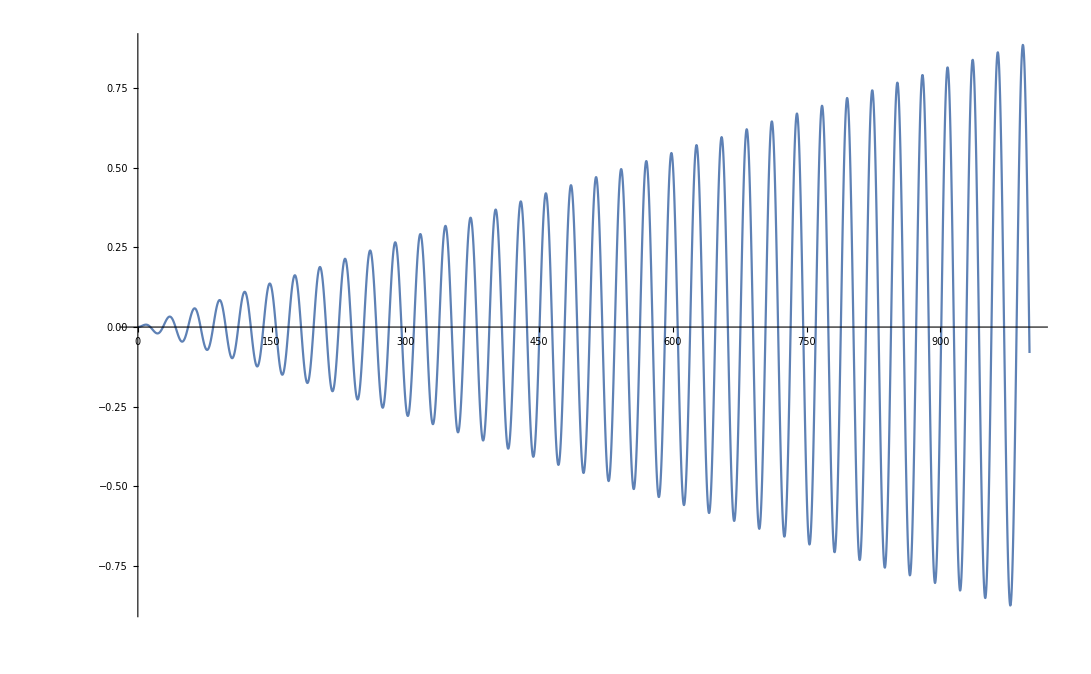

```mathematica
Plot[{(NMα[n]/.{β-> 1/ 4})-Theoα[n]}, {n, 0, 1000}]
```

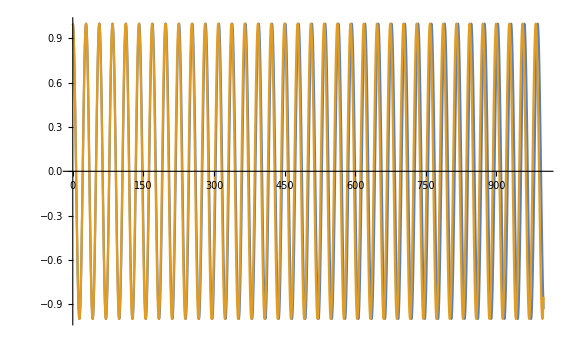

```mathematica
Plot[{simplifiedNMα[n], Theoα[n]}, {n, 0, 1000}, ImageSize->Large]
```

```mathematica
simplifiedNMα[n]
```

Cos[n ArcTan[(8 √5)/79]]

```mathematica
Theoα[n]
```

Cos[n/(2 √5)]

```mathematica
(1 /(2 * Sqrt[5]) - ArcTan[(8 √5)/79] ) / (1 / (2 * Sqrt[5]))// N
```

0.00413569

```mathematica
h
```

1/100